```mathematica
SetDirectory["C:\\Users\\benja\\OneDrive\\Documents\\GitHub\\KhovanovLaplacian\\basic_khovanov_testing"]
<< KnotTheory`
<< KhovanovLaplacian`
```

C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing

Get::path: ParentDirectory[File] in $Path is not a string.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ParentDirectory[File],KnotTheory].

FileInformation::badfile: The specified argument, ToFileName[ParentDirectory[File],KnotTheory], should be a valid string or File.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ToFileName[{File,WikiLink,mathematica}],KnotTheory].

FileInformation::badfile: The specified argument, ToFileName[ToFileName[{File,WikiLink,mathematica}],KnotTheory], should be a valid string or File.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ToFileName[{File,QuantumGroups}],KnotTheory].

General::stop: Further output of ToFileName::strse will be suppressed during this calculation.

FileInformation::badfile: The specified argument, ToFileName[ToFileName[{File,QuantumGroups}],KnotTheory], should be a valid string or File.

General::stop: Further output of FileInformation::badfile will be suppressed during this calculation.

ReplaceAll::reps: {AbsoluteFileName→C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing\KnotTheory,AbsoluteShortFileName→C:\Users\benja\OneDrive\DOCUME~1\GitHub\KHOVAN~1\BASIC_~1\KNOTTH~1,Archive→True,BlockCount→Missing[NotAvailable],BlockSize→Missing[NotAvailable],ByteCount→12288,Compressed→Missing[NotAvailable],CreationDate→DateObject[{2024,3,13,15,49,29.},Instant,Gregorian,-5.],DirectoryName→C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing,Encrypted→Missing[NotAvailable],«23»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ParentDirectory::nums: Argument File/.{AbsoluteFileName→C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing\KnotTheory,AbsoluteShortFileName→C:\Users\benja\OneDrive\DOCUME~1\GitHub\KHOVAN~1\BASIC_~1\KNOTTH~1,Archive→True,BlockCount→Missing[NotAvailable],BlockSize→Missing[NotAvailable],ByteCount→12288,Compressed→Missing[NotAvailable],CreationDate→DateObject[{2024,3,13,15,49,29.},Instant,Gregorian,-5.],DirectoryName→C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing,Encrypted→Missing[NotAvailable],«23»} should be a positive machine-size integer, a nonempty string, or a File specification.

Loading KnotTheory` version of September 6, 2014, 13:37:37.2841.
Read more at http://katlas.org/wiki/KnotTheory.

Get::path: ParentDirectory[File] in $Path is not a string.

General::stop: Further output of Get::path will be suppressed during this calculation.

Get::noopen: Cannot open WikiLink`.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

DeclarePackage::aldec: Symbol CreateWikiConnection in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,WikiUploadFile,WikiUserName,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,«2»}] has already been declared.

Get::noopen: Cannot open WikiLink`.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

DeclarePackage::aldec: Symbol WikiGetPageText in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,WikiUploadFile,WikiUserName,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,«2»}] has already been declared.

Get::noopen: Cannot open WikiLink`.

General::stop: Further output of Get::noopen will be suppressed during this calculation.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

General::stop: Further output of Needs::nocont will be suppressed during this calculation.

DeclarePackage::aldec: Symbol WikiGetPageTexts in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,WikiUploadFile,WikiUserName,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,«2»}] has already been declared.

General::stop: Further output of DeclarePackage::aldec will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[WikiGetPageText[Invariant_Definition_Table],<tr>].

StringSplit::argb: StringSplit called with 0 arguments; between 1 and 3 arguments are expected.

Join::heads: Heads StringSplit and List at positions 1 and 2 are expected to be the same.

Loading KhovanovLaplacian`...

PD[X[1,5,2,4],X[5,3,6,2],X[3,1,4,6]]

KnotTheory::credits: DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004.

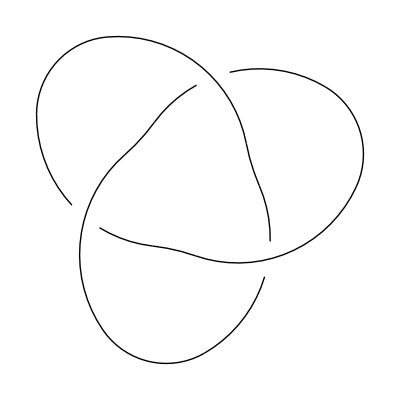

qSpectraAllEigs[0,1] = {0.}

qSpectraAllEigs[0,3] = {6.,0.}

qSpectraAllEigs[0,5] = {3.}

qSpectraAllEigs[1,3] = {6.,3.,3.}

qSpectraAllEigs[1,5] = {6.,6.,3.}

qSpectraAllEigs[2,3] = {3.,3.,3.}

qSpectraAllEigs[2,5] = {6.,6.,5.,2.,2.,-2.38512×10^-16}

qSpectraAllEigs[2,7] = {4.,1.,1.}

qSpectraAllEigs[3,3] = {3.}

qSpectraAllEigs[3,5] = {5.,2.,2.}

qSpectraAllEigs[3,7] = {4.,1.,1.}

qSpectraAllEigs[3,9] = {0.}

{{{0.},{6.,0.},{3.}},{{6.,3.,3.},{6.,6.,3.}},{{3.,3.,3.},{6.,6.,5.,2.,2.,-2.38512×10^-16},{4.,1.,1.}},{{3.},{5.,2.,2.},{4.,1.,1.},{0.}}}

```mathematica
trefoil = PD[X[1,5,2,4],X[5,3,6,2],X[3,1,4,6]] (*x-z projection leading to right handed trefoil with standard diagram*)
Show[DrawPD[trefoil]]
s1 = qSpectraAllEigs[trefoil]
```

## Form an Interesting Dirac operator, quantum grading 3 seems large but promising, quantum grading 7 maybe a little better? Let’s check the dimensions

```mathematica
CC[trefoil,-1,3]
CC[trefoil,0,3]
CC[trefoil,1,3]
CC[trefoil,2,3]
CC[trefoil,3,3]
CC[trefoil,4,3]
```

{0}

{v[0,0,0] vm[2] vp[1],v[0,0,0] vm[1] vp[2]}

{v[0,0,1] vm[1],v[0,1,0] vm[1],v[1,0,0] vm[1]}

{v[0,1,1] vm[1] vm[3],v[1,0,1] vm[1] vm[2],v[1,1,0] vm[1] vm[2]}

{v[1,1,1] vm[1] vm[2] vm[3]}

{0}

```mathematica
GetDQ[trefoil,-1,3]// MatrixForm
GetDQ[trefoil,0,3]// MatrixForm
GetDQ[trefoil,1,3]// MatrixForm
GetDQ[trefoil,2,3]// MatrixForm
GetDQ[trefoil,3,3]// MatrixForm
GetDQ[trefoil,4,3] // MatrixForm
```

(0)

(0
0)

(1 | 1
1 | 1
1 | 1)

(1 | -1 | 0
1 | 0 | -1
0 | 1 | -1)

(1 | -1 | 1)

(0)

```mathematica
Dirac = ArrayFlatten[{{0,                                                             GetDQ[trefoil,1,3],                          0,                                                                                                            0},
			   {Transpose[GetDQ[trefoil,1,3]], 0,                                                                  GetDQ[trefoil,2,3],                                                                   0},
                                {0,                                                                  Transpose[GetDQ[trefoil,2,3]], 0,                                                                  GetDQ[trefoil,3,3]},
			{0,                                                                      0,                                                                   Transpose[GetDQ[trefoil,3,3]],                                         0}}]
Dirac//MatrixForm
```

ArrayFlatten::match: … fails the matching condition for ArrayFlatten[a,n]: if b = a[[i_1,i_2,...,i_n]], c = a[[j_1,j_2,...,j_n]], Head[a] == Head[b] == Head[c], Length[Dimensions[b]] >= n, Length[Dimensions[c]] >= n, and i_k = j_k, then Dimensions[b][[k]] must equal Dimensions[c][[k]]. Here the condition fails for k = 1 and i_k = j_k = 2.

ArrayFlatten[{{0,SparseArray[…],0,0},{SparseArray[…],0,SparseArray[…],0},{0,SparseArray[…],0,SparseArray[…]},{0,0,SparseArray[…],0}}]

ArrayFlatten[{{0,SparseArray[…],0,0},{SparseArray[…],0,SparseArray[…],0},{0,SparseArray[…],0,SparseArray[…]},{0,0,SparseArray[…],0}}]

```mathematica
Dirac = ArrayFlatten[{{0,                                                             GetDQ[trefoil,1,3],                          0},
			   {Transpose[GetDQ[trefoil,1,3]], 0,                                                                  GetDQ[trefoil,2,3]},
                                {0,                                                                  Transpose[GetDQ[trefoil,2,3]], 0}}]
Dirac//MatrixForm
```

ArrayFlatten::match: … fails the matching condition for ArrayFlatten[a,n]: if b = a[[i_1,i_2,...,i_n]], c = a[[j_1,j_2,...,j_n]], Head[a] == Head[b] == Head[c], Length[Dimensions[b]] >= n, Length[Dimensions[c]] >= n, and i_k = j_k, then Dimensions[b][[k]] must equal Dimensions[c][[k]]. Here the condition fails for k = 1 and i_k = j_k = 2.

ArrayFlatten[{{0,SparseArray[…],0},{SparseArray[…],0,SparseArray[…]},{0,SparseArray[…],0}}]

ArrayFlatten[{{0,SparseArray[…],0},{SparseArray[…],0,SparseArray[…]},{0,SparseArray[…],0}}]

```mathematica
Dirac1 = ArrayFlatten[{{0,                                                             GetDQ[trefoil,1,3]},
			   {Transpose[GetDQ[trefoil,1,3]], 0}}]
Dirac1//MatrixForm
```

SparseArray[…]

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

```mathematica
blockzero[a_Integer,b_Integer]:= ConstantArray[0,{Length[CC[trefoil,a,3]],Length[CC[trefoil,b,3]]}]
```

```mathematica
Dirac = ArrayFlatten[{{blockzero[0,0],                                                             Transpose[GetDQ[trefoil,1,3]],                          blockzero[0,2]},
			   {GetDQ[trefoil,1,3], blockzero[1,1],                                                                  Transpose[GetDQ[trefoil,2,3]]},
                                {blockzero[2,0],                                                                  GetDQ[trefoil,2,3], blockzero[2,2]}}]//MatrixForm
```

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0 | -1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 0 | -1 | -1
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0)

```mathematica
GetDQ[trefoil,1,3]// MatrixForm
blockzero[0,0] // MatrixForm
ArrayFlatten[{{blockzero[0,0],Transpose[ GetDQ[trefoil,1,3]]},
			{GetDQ[trefoil,1,3],blockzero[1,1]}}] // MatrixForm
```

(1 | 1
1 | 1
1 | 1)

(0 | 0
0 | 0)

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

```mathematica
blockzero[1,1] // MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
Dirac1 = ArrayFlatten[{{blockzero[0,0],Transpose[ GetDQ[trefoil,1,3]]},
			{GetDQ[trefoil,1,3],blockzero[1,1]}}]
Dirac1//MatrixForm
(*
	Form dirac2 as
	[Dirac1    
		]
*)
blockzero[0,2] // MatrixForm
GetDQ[trefoil,2,3] // MatrixForm
ArrayFlatten[{{blockzero[0,2]},{Transpose[GetDQ[trefoil,2,3]]}}] // MatrixForm
ArrayFlatten[{{blockzero[2,0],GetDQ[trefoil,2,3]}}]// MatrixForm
```

{{0,0,1,1,1},{0,0,1,1,1},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}}

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

(0 | 0 | 0
0 | 0 | 0)

(1 | -1 | 0
1 | 0 | -1
0 | 1 | -1)

(0 | 0 | 0
0 | 0 | 0
1 | 1 | 0
-1 | 0 | 1
0 | -1 | -1)

(0 | 0 | 1 | -1 | 0
0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 1 | -1)

```mathematica
Dirac2 = ArrayFlatten[{{Dirac1, ArrayFlatten[{{blockzero[0,2]},{Transpose[GetDQ[trefoil,2,3]]}}]},
					{ArrayFlatten[{{blockzero[2,0],GetDQ[trefoil,2,3]}}], blockzero[2,2]}}]
Dirac2 //MatrixForm
```

{{0,0,1,1,1,0,0,0},{0,0,1,1,1,0,0,0},{1,1,0,0,0,1,1,0},{1,1,0,0,0,-1,0,1},{1,1,0,0,0,0,-1,-1},{0,0,1,-1,0,0,0,0},{0,0,1,0,-1,0,0,0},{0,0,0,1,-1,0,0,0}}

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0 | -1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 0 | -1 | -1
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0)

```mathematica
Dirac2.Dirac2 // MatrixForm
qLapNew[trefoil,0,3]// MatrixForm
qLapNew[trefoil,1,3]// MatrixForm
qLapNew[trefoil,2,3]// MatrixForm
qLapNew[trefoil,3,3]// MatrixForm
```

(3 | 3 | 0 | 0 | 0 | 0 | 0 | 0
3 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 4 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 1 | -1
0 | 0 | 0 | 0 | 0 | 1 | 2 | 1
0 | 0 | 0 | 0 | 0 | -1 | 1 | 2)

(3 | 3
3 | 3)

(4 | 1 | 1
1 | 4 | 1
1 | 1 | 4)

(3 | 0 | 0
0 | 3 | 0
0 | 0 | 3)

(3)

```mathematica
lengths = Length[CC[trefoil,#,3]] &/@ Range[-nm[trefoil],Length[trefoil]-nm[trefoil]]
subtotals = Accumulate[lengths]
lengths[[1]]
lengths[[2]]
-nm[trefoil]
```

{2,3,3,1}

{2,5,8,9}

2

3

0

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

```mathematica
Dirac = ConstantArray[0,{Total[lengths],Total[lengths]}]
Dirac //MatrixForm
Dirac[[1;;lengths[[1]],subtotals[[1]]+1;;subtotals[[2]]]] = Transpose[GetDQ[trefoil,1,3]];
Dirac // MatrixForm
Dirac[[subtotals[[1]]+1;;subtotals[[2]],subtotals[[2]]+1;;subtotals[[3]]]]= Transpose[GetDQ[trefoil,2,3]];
Dirac // MatrixForm
Dirac[[subtotals[[2]]+1;;subtotals[[3]],subtotals[[3]]+1;;subtotals[[4]]]]= Transpose[GetDQ[trefoil,3,3]];
Dirac = Dirac + Transpose[Dirac];
Dirac // MatrixForm
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | 0)

```mathematica
Dirac = ConstantArray[0,{Total[lengths],Total[lengths]}]
Dirac //MatrixForm
Dirac[[1;;lengths[[1]],subtotals[[1]]+1;;subtotals[[2]]]] = Transpose[GetDQ[trefoil,1,3]];
Do[Dirac[[subtotals[[i-2]]+1;;subtotals[[i-1]],subtotals[[i-1]]+1;;subtotals[[i]]]]=Transpose[GetDQ[trefoil,i-1,3]],{i,3,4}]
Dirac //MatrixForm
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
getDirac[L_PD,r_Integer,q_Integer] := (
lengths = Length[CC[L,#,q]] &/@ Range[-nm[L],Min[r,Length[L]-nm[L]]];
subtotals = Accumulate[lengths];
Dirac = ConstantArray[0,{Total[lengths],Total[lengths]}];
Dirac[[1;;lengths[[1]],subtotals[[1]]+1;;subtotals[[2]]]] = Transpose[GetDQ[L,-nm[L]+1,q]]; (*caution: unclear if correct shif for DQ is -nm[L]+1 or something else*)
Do[Dirac[[subtotals[[i-2]]+1;;subtotals[[i-1]],subtotals[[i-1]]+1;;subtotals[[i]]]]=Transpose[GetDQ[L,-nm[L]+i-1,q]],{i,3,Length[lengths]}];
Dirac = Dirac + Transpose[Dirac];
Dirac
)
getDirac[trefoil,4,5]//MatrixForm
Eigenvalues[getDirac[trefoil,4,3]]
```

(0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0)

{-√6,√6,-√3,-√3,-√3,√3,√3,√3,0}